```mathematica
Needs["MFGraphs`"]
```

Get::noopen: Cannot open MFGraphs`.

Needs::nocont: Context MFGraphs` was not created when Needs was evaluated.

$Failed

```mathematica
Cases[$Packages,"MFGraphs`"]
```

{MFGraphs`}

```mathematica
Names["MFGraphs`*"]
```

{A,alpha,AtHead,AtTail,A$,beta,Data,DataG,DataToEquations,DataToGraph,EE,EqEliminatorX,eqs,Eqs,eqs$,F,FixedPointSolverStepX,g,globalrules,g$61521,H,I1,I2,Intg,listeqs,listeqs$,m,MFGEquations,m$,n,newrules,newrules$,newrules$18042,newrules$18051,newrules$18060,newrules$2481,newrules$2493,newrules$28748,newrules$28755,newrules$28764,newsolve,newsolve$,nonlinear,nonlinearsystem,nonlinear$,OtherWay,p,Parameters,p$,RR,rules,rules$,S1,S10,S11,S12,S13,S14,S15,S16,S2,S3,S4,S5,S6,S7,S8,S9,startrulesX,StartSolverX,system,system$,Test,TransitionsAt,triple2path,U1,U2,UU,V,V$61521,W,W$61521,x,x$}

```mathematica
Data=DataG[26];
```

```mathematica
MFGEquations=DataToEquations[Data];
```

Solving the linear equations

Done.

```mathematica
Keys[MFGEquations]
```

{BG,EntranceVertices,InwardVertices,InEdges,ExitVertices,OutwardVertices,OutEdges,AuxiliaryGraph,FG,VL,EL,BEL,FVL,AllTransitions,IncomingEdges[k_],OutgoingEdges[k_],NoDeadEnds,NoDeadStarts,jargs,js,jvars,jts,jtvars,uargs,us,uvars,CurrentCompCon[a_ -> b_],EqCurrentCompCon,TransitionCompCon,EqTransitionCompCon,Compu,EqCompCon,EqAllComp,EqPosCon,CurrentSplitting,CurrentGathering,EqBalanceSplittingCurrents,EqBalanceGatheringCurrents,EntryArgs,EntryDataAssociation,EqEntryIn,NonZeroEntryCurrents,ExitCosts,ExitValues,EqExitValues,SwitchingCosts,OutRules,InRules,Transu,EqSwitchingConditions,EqValueAuxiliaryEdges,EqAll,jays,Nrhs,Nlhs,Boo,EqAllCompRules,EqAllRules,EqAllAll,EqAllAllSimple}

```mathematica
sys=MFGEquations["EqAllAll"]//Simplify
```

NonNegative[j36]&&NonNegative[j37]&&NonNegative[j38]&&NonNegative[j39]&&NonNegative[j40]&&NonNegative[j41]&&NonNegative[jt42]&&NonNegative[jt43]&&NonNegative[jt44]&&NonNegative[jt45]&&j39==jt42&&j38==jt43&&j36==jt44&&j40==jt45&&j36==jt43&&j41==jt42&&j39==jt45&&j37==jt44&&j38==80&&u50==15&&u51≤u46&&u46≤∞&&u47≤∞&&u49≤u47&&u48==u51&&u47==u50&&(j39==0||j36==0)&&(j40==0||j37==0)&&(j41==0||j38==0)&&(jt42==0||jt43==0)&&(jt44==0||jt45==0)&&jt42==0&&(jt43==0||u46==u51)&&(jt44==0||u47==u49)&&jt45==0

```mathematica
MFGEquations["EqAllAllRules"]
```

Missing[KeyAbsent,EqAllAllRules]

```mathematica
MFGEquations["CurrentCompCon[a_ -> b_]"][1->2]
```

j39==0||j36==0

```mathematica
MFGEquations["EqCurrentCompCon"]
```

(j39==0||j36==0)&&(j40==0||j37==0)&&(j41==0||j38==0)

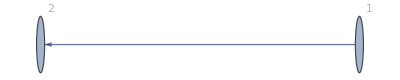
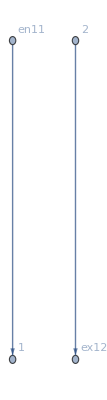
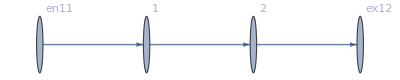
<|BG→-Graphics-,EntranceVertices→{1},InwardVertices→<|1→en11|>,InEdges→{en11->1},ExitVertices→{2},OutwardVertices→<|2→ex12|>,OutEdges→{2->ex12},AuxiliaryGraph→-Graphics-,FG→-Graphics-,VL→{1,2},EL→{1->2,2->ex12,en11->1},BEL→{1->2},FVL→{1,2,en11,ex12},AllTransitions→{{1,1->2,en11->1},{1,en11->1,1->2},{2,1->2,2->ex12},{2,2->ex12,1->2}},IncomingEdges→MFGraphs`Private`IncomingEdges$4380,OutgoingEdges→MFGraphs`Private`OutgoingEdges$4380,NoDeadEnds→{{1,1->2},{1,en11->1},{2,1->2},{2,2->ex12}},NoDeadStarts→{{2,1->2},{en11,en11->1},{1,1->2},{ex12,2->ex12}},jargs→{{2,1->2},{ex12,2->ex12},{1,en11->1},{1,1->2},{2,2->ex12},{en11,en11->1}},js→{j13,j14,j15,j16,j17,j18},jvars→<|{2,1->2}→j13,{ex12,2->ex12}→j14,{1,en11->1}→j15,{1,1->2}→j16,{2,2->ex12}→j17,{en11,en11->1}→j18|>,jts→{jt19,jt20,jt21,jt22},jtvars→<|{1,1->2,en11->1}→jt19,{1,en11->1,1->2}→jt20,{2,1->2,2->ex12}→jt21,{2,2->ex12,1->2}→jt22|>,uargs→{{1,1->2},{2,2->ex12},{en11,en11->1},{2,1->2},{ex12,2->ex12},{1,en11->1}},us→{u23,u24,u25,u26,u27,u28},uvars→<|{1,1->2}→u23,{2,2->ex12}→u24,{en11,en11->1}→u25,{2,1->2}→u26,{ex12,2->ex12}→u27,{1,en11->1}→u28|>,CurrentCompCon→MFGraphs`Private`CurrentCompCon$4380,EqCurrentCompCon→(j16==0||j13==0)&&(j17==0||j14==0)&&(j18==0||j15==0),TransitionCompCon→MFGraphs`Private`TransitionCompCon$4380,EqTransitionCompCon→(jt19==0||jt20==0)&&(jt21==0||jt22==0),Compu→MFGraphs`Private`Compu$4380,EqCompCon→jt19==0&&(jt20==0||-u23+u28==0)&&(jt21==0||-u24+u26==0)&&jt22==0,EqAllComp→(j16==0||j13==0)&&(j17==0||j14==0)&&(j18==0||j15==0)&&(jt19==0||jt20==0)&&(jt21==0||jt22==0)&&jt19==0&&(jt20==0||-u23+u28==0)&&(jt21==0||-u24+u26==0)&&jt22==0,EqPosCon→NonNegative[j13]&&NonNegative[j14]&&NonNegative[j15]&&NonNegative[j16]&&NonNegative[j17]&&NonNegative[j18]&&NonNegative[jt19]&&NonNegative[jt20]&&NonNegative[jt21]&&NonNegative[jt22],CurrentSplitting→MFGraphs`Private`CurrentSplitting$4380,CurrentGathering→MFGraphs`Private`CurrentGathering$4380,EqBalanceSplittingCurrents→j16==jt19&&j15==jt20&&j13==jt21&&j17==jt22,EqBalanceGatheringCurrents→j13==jt20&&j18==jt19&&j16==jt22&&j14==jt21,EntryArgs→{{1,en11->1}},EntryDataAssociation→<|{1,en11->1}→80|>,EqEntryIn→j15==80,NonZeroEntryCurrents→True,ExitCosts→<|ex12→15|>,ExitValues→MFGraphs`Private`ExitValues$4380,EqExitValues→u27==15,SwitchingCosts→<|{1,1->2,en11->1}→∞,{1,en11->1,1->2}→0,{2,1->2,2->ex12}→0,{2,2->ex12,1->2}→∞,{2,2->ex12,2->ex12}→∞,{2,2->ex12,en11->1}→∞,{1,en11->1,en11->1}→∞|>,OutRules→{{2,2->ex12,1->2}→∞,{2,2->ex12,2->ex12}→∞,{2,2->ex12,en11->1}→∞},InRules→{{1,1->2,en11->1}→∞,{1,en11->1,en11->1}→∞},Transu→MFGraphs`Private`Transu$4380,EqSwitchingConditions→u28≤u23&&u23≤∞&&u24≤∞&&u26≤u24,EqValueAuxiliaryEdges→-u25+u28==0&&-u24+u27==0,EqAll→NonNegative[j13]&&NonNegative[j14]&&NonNegative[j15]&&NonNegative[j16]&&NonNegative[j17]&&NonNegative[j18]&&NonNegative[jt19]&&NonNegative[jt20]&&NonNegative[jt21]&&NonNegative[jt22]&&j16==jt19&&j15==jt20&&j13==jt21&&j17==jt22&&j13==jt20&&j18==jt19&&j16==jt22&&j14==jt21&&j15==80&&u27==15&&u28≤u23&&u23≤∞&&u24≤∞&&u26≤u24&&-u25+u28==0&&-u24+u27==0,jays→<|1->2→j13-j16|>,Nrhs→{j13-j16+Intg[j13-j16]},Nlhs→{j13-j16-u23+u26},Boo→MFGraphs`Private`Boo$4380,EqAllCompRules→(j16==0||j13==0)&&(j17==0||j14==0)&&j18==0&&(jt19==0||jt20==0)&&(jt21==0||jt22==0)&&jt19==0&&(jt20==0||-u23+u28==0)&&(jt21==0||-u24+u26==0)&&jt22==0,EqAllRules→NonNegative[j13]&&NonNegative[j14]&&NonNegative[j16]&&NonNegative[j17]&&NonNegative[j18]&&NonNegative[jt19]&&NonNegative[jt20]&&NonNegative[jt21]&&NonNegative[jt22]&&j16==jt19&&80==jt20&&j13==jt21&&j17==jt22&&j13==jt20&&j18==jt19&&j16==jt22&&j14==jt21&&u28≤u23&&u23≤∞&&u24≤∞&&u26≤u24&&-u25+u28==0&&15-u24==0,EqAllAll→NonNegative[j13]&&NonNegative[j14]&&NonNegative[j15]&&NonNegative[j16]&&NonNegative[j17]&&NonNegative[j18]&&NonNegative[jt19]&&NonNegative[jt20]&&NonNegative[jt21]&&NonNegative[jt22]&&j16==jt19&&j15==jt20&&j13==jt21&&j17==jt22&&j13==jt20&&j18==jt19&&j16==jt22&&j14==jt21&&j15==80&&u27==15&&u28≤u23&&u23≤∞&&u24≤∞&&u26≤u24&&-u25+u28==0&&-u24+u27==0&&(j16==0||j13==0)&&(j17==0||j14==0)&&(j18==0||j15==0)&&(jt19==0||jt20==0)&&(jt21==0||jt22==0)&&jt19==0&&(jt20==0||-u23+u28==0)&&(jt21==0||-u24+u26==0)&&jt22==0,EqAllAllSimple→MFGraphs`Private`EqAllAllSimple$4380|>

```mathematica
MFGEquations
```

```mathematica
CriticalCongestionSolve[MFGEquations_Association]:= Module[{variables},Reduce.... Just return the solution (us, js, jts)];
```

```mathematica
Reformat results from above function:
```

```mathematica
Compi
```

```mathematica
jays=AssociationThread[MFGEquations["BEL"],(MFGEquations["jvars"][AtHead[#]]-MFGEquations["jvars"][AtTail[#]]&)/@MFGEquations["BEL"]];
```

```mathematica
Parameters
```

<|alpha→0.5,beta→2,g[m]→Function[{m},m^beta],W[x,A]→Function[{x,A},A Sin[2 π (x+1/4)]^2],V[x]→Function[{x$},W$4172[x$,1/2]],H[x,p,m]→Function[{x$,p$,m$},p$^2/(2 m$^alpha)+V$4172[x$]-g$4172[m$]]|>

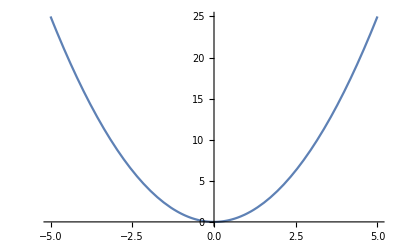

```mathematica
Plot[Parameters["g[m]"][x],{x,-5,5}]
```

```mathematica
Normal[%33]
```

{alpha→0.5,beta→2,g[m]→Function[{m},m^beta],W[x,A]→Function[{x,A},A Sin[2 π (x+1/4)]^2],V[x]→Function[{x$},W$4172[x$,1/2]],H[x,p,m]→Function[{x$,p$,m$},p$^2/(2 m$^alpha)+V$4172[x$]-g$4172[m$]]}

```mathematica
jays
```

<|1->2→j113-j119,2->3→j114-j120,2->4→j115-j121|>

```mathematica
List@@BooleanConvert@MFGEquations["EqAllComp"]
```

{j74==0&&j75==0&&j76==0&&j77==0&&j78==0&&j79==0&&jt86==0&&jt87==0&&jt88==0&&jt89==0&&jt90==0&&jt91==0&&jt92==0&&jt93==0&&jt94==0&&jt95==0&&jt96==0&&jt97==0,j74==0&&j75==0&&j76==0&&j77==0&&j78==0&&j79==0&&jt86==0&&jt87==0&&jt88==0&&jt89==0&&jt90==0&&jt91==0&&jt92==0&&jt93==0&&jt94==0&&jt95==0&&jt97==0&&-u102+u106==0,13821,j80==0&&j81==0&&j82==0&&j83==0&&j84==0&&j85==0&&jt86==0&&jt90==0&&jt92==0&&jt93==0&&jt95==0&&jt97==0&&-u100+u104==0&&-u101+u105==0&&-u102+u106==0&&u109-u98==0&&u104-u99==0&&-u100+u99==0}
 |  |  |  |

```mathematica
MFGEquations["uvars"]
```

<|{1,1->2}→u23,{2,2->ex12}→u24,{en11,en11->1}→u25,{2,1->2}→u26,{ex12,2->ex12}→u27,{1,en11->1}→u28|>

```mathematica
MFGEquations["EL"]
```

{1->2,2->ex12,en11->1}

```mathematica
MFGEquations["uvars"]/@AtHead /@ MFGEquations["EL"]
```

{u26,u27,u28}

```mathematica
MFGEquations["uvars"]/@AtHead /@ MFGEquations["BEL"]
```

{u26}

```mathematica
Keys[MFGEquations]
```

{BG,EntranceVertices,InwardVertices,InEdges,ExitVertices,OutwardVertices,OutEdges,AuxiliaryGraph,FG,VL,EL,BEL,FVL,AllTransitions,IncomingEdges,OutgoingEdges,NoDeadEnds,NoDeadStarts,jargs,js,jvars,jts,jtvars,uargs,us,uvars,CurrentCompCon,EqCurrentCompCon,TransitionCompCon,EqTransitionCompCon,Compu,EqCompCon,EqAllComp,EqPosCon,CurrentSplitting,CurrentGathering,EqBalanceSplittingCurrents,EqBalanceGatheringCurrents,EntryArgs,EntryDataAssociation,EqEntryIn,NonZeroEntryCurrents,ExitCosts,ExitValues,EqExitValues,SwitchingCosts,OutRules,InRules,Transu,EqSwitchingConditions,EqValueAuxiliaryEdges,EqAll,jays,Nrhs,Nlhs,Boo,EqAllCompRules,EqAllRules,EqAllAll,EqAllAllSimple}

### Using the new functions in IterationFunction.m

```mathematica
Data=DataG[17];
MFGEquations=DataToEquations[Data];
```

Solving the linear equations

Done.

#### This is the reduction of the system (in place of Reduce)

```mathematica
globalrules={};
reduced = FixedPoint[EqEliminatorX,MFGEquations["EqAllCompRules"]&&MFGEquations["EqAllRules"],10];
AssociateTo[MFGEquations,{"reduced"->reduced,"globalrules"->globalrules}];
```

```mathematica
reduced
globalrules
```

(2-jt29==0||-j18+jt29==0)&&(jt29==0||j18-jt29==0)&&(j18-jt29==0||-j18+jt29==0)&&(2-jt29==0||-u39+u44==0)&&(jt29==0||-u40+u44==0)&&(-j18+jt29==0||u39-u44==0)&&(j18-jt29==0||u39-u40==0)&&(j18-jt29==0||u40-u44==0)&&(-j18+jt29==0||-u39+u40==0)&&(2-j18==0||-2+u45==0)&&(j18==0||-1+u46==0)&&NonNegative[2-j18]&&NonNegative[j18]&&NonNegative[2-j18]&&NonNegative[j18]&&NonNegative[2-jt29]&&NonNegative[jt29]&&NonNegative[-j18+jt29]&&NonNegative[j18-jt29]&&NonNegative[j18-jt29]&&NonNegative[-j18+jt29]&&NonNegative[2-j18]&&NonNegative[j18]&&u43≤u43&&u43≤∞&&u39≤u44&&u40≤u44&&u44≤u39&&u40≤u39&&u44≤u40&&u39≤u40&&u45≤2&&u46≤1

{j14→2,j15→2-j18,j16→j18,j17→2-j18,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→2,jt28→2-jt29,jt30→-j18+jt29,jt31→j18-jt29,jt32→j18-jt29,jt33→-j18+jt29,jt34→2-j18,jt35→0,jt36→j18,jt37→0,u38→u43,u41→2,u42→1,u49→u43}

#### The critical congestion case (general numeric solver)

```mathematica
startrulesX=StartSolverX[MFGEquations];
AssociateTo[MFGEquations,"CriticalCongestionSolution"->First[startrulesX]];
```

```mathematica
First @startrulesX
```

{j14→2,j15→1/2,j16→3/2,j17→1/2,j18→3/2,j19→2,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→2,jt28→1/2,jt29→3/2,jt30→0,jt31→0,jt32→0,jt33→0,jt34→1/2,jt35→0,jt36→3/2,jt37→0,u38→9/2,u39→5/2,u40→5/2,u41→2,u42→1,u43→9/2,u44→5/2,u45→2,u46→1,u47→2,u48→1,u49→9/2}

#### Non-linear case

```mathematica
globalrules
```

{j14→2,j15→2-j18,j16→j18,j17→2-j18,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→2,jt28→2-jt29,jt30→-j18+jt29,jt31→j18-jt29,jt32→j18-jt29,jt33→-j18+jt29,jt34→2-j18,jt35→0,jt36→j18,jt37→0,u38→u43,u41→2,u42→1,u49→u43}

```mathematica
MFGEquations["Nrhs"]
```

{j14-j20+MFGraphs`Private`Intg[j14-j20],j15-j21+MFGraphs`Private`Intg[j15-j21],j16-j22+MFGraphs`Private`Intg[j16-j22]}

```mathematica
j14-j20/.globalrules
```

2

```mathematica
Keys @ Parameters
```

{alpha,beta,g[m],W[x,A],V[x],H[x,p,m]}

```mathematica
alpha
```

0.5

```mathematica
Parameters["alpha"]
```

0.5

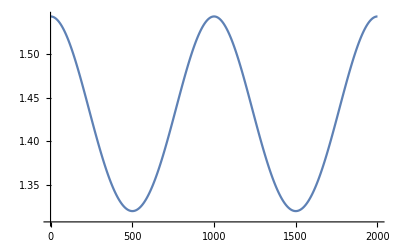

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

```mathematica
Plot[FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]&,{x,0,1}]
```

-Graphics-

```mathematica
h=Intg[2]
```

-1.67538

```mathematica
h
```

```mathematica
MFGEquations["Nrhs"]/.globalrules
```

{2-2 NIntegrate[1/(MFGraphs`Private`F[2,MFGraphs`Private`x])^(1-MFGraphs`Private`Parameters[alpha]),{MFGraphs`Private`x,0,1}],2-j18+MFGraphs`Private`Intg[2-j18],j18+MFGraphs`Private`Intg[j18]}

```mathematica
FixedPointSolverStepX[MFGEquations][startrulesX]
```

2-u43+u44==2-2 NIntegrate[1/(MFGraphs`Private`F[2,MFGraphs`Private`x])^(1-MFGraphs`Private`Parameters[alpha]),{MFGraphs`Private`x,0,1}]&&2-j18-u39+u45==1/2-1/2 NIntegrate[1/(MFGraphs`Private`F[1/2,MFGraphs`Private`x])^(1-MFGraphs`Private`Parameters[alpha]),{MFGraphs`Private`x,0,1}]&&j18-u40+u46==3/2-3/2 NIntegrate[1/(MFGraphs`Private`F[3/2,MFGraphs`Private`x])^(1-MFGraphs`Private`Parameters[alpha]),{MFGraphs`Private`x,0,1}]

2-u43+u44==2-2 NIntegrate[1/(MFGraphs`Private`F[2,MFGraphs`Private`x])^(1-MFGraphs`Private`Parameters[alpha]),{MFGraphs`Private`x,0,1}]&&2-j18-u39+u45==1/2-1/2 NIntegrate[1/(MFGraphs`Private`F[1/2,MFGraphs`Private`x])^(1-MFGraphs`Private`Parameters[alpha]),{MFGraphs`Private`x,0,1}]&&j18-u40+u46==3/2-3/2 NIntegrate[1/(MFGraphs`Private`F[3/2,MFGraphs`Private`x])^(1-MFGraphs`Private`Parameters[alpha]),{MFGraphs`Private`x,0,1}]&&(2-jt29==0||-j18+jt29==0)&&(jt29==0||j18-jt29==0)&&(j18-jt29==0||-j18+jt29==0)&&(2-jt29==0||-u39+u44==0)&&(jt29==0||-u40+u44==0)&&(-j18+jt29==0||u39-u44==0)&&(j18-jt29==0||u39-u40==0)&&(j18-jt29==0||u40-u44==0)&&(-j18+jt29==0||-u39+u40==0)&&(2-j18==0||-2+u45==0)&&(j18==0||-1+u46==0)&&NonNegative[2-j18]&&NonNegative[j18]&&NonNegative[2-j18]&&NonNegative[j18]&&NonNegative[2-jt29]&&NonNegative[jt29]&&NonNegative[-j18+jt29]&&NonNegative[j18-jt29]&&NonNegative[j18-jt29]&&NonNegative[-j18+jt29]&&NonNegative[2-j18]&&NonNegative[j18]&&u43≤u43&&u43≤∞&&u39≤u44&&u40≤u44&&u44≤u39&&u40≤u39&&u44≤u40&&u39≤u40&&u45≤2&&u46≤1

2-u43+u44==2-2 NIntegrate[1/(MFGraphs`Private`F[2,MFGraphs`Private`x])^(1-MFGraphs`Private`Parameters[alpha]),{MFGraphs`Private`x,0,1}]

{j14→2,j15→2-j18,j16→j18,j17→2-j18,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→2,jt28→2-jt29,jt30→-j18+jt29,jt31→j18-jt29,jt32→j18-jt29,jt33→-j18+jt29,jt34→2-j18,jt35→0,jt36→j18,jt37→0,u38→u43,u41→2,u42→1,u49→u43}